## Resources

https://community.wolfram.com/groups/-/m/t/1378454

## Basics

Kernel

stores values

runs computation

FrontEnd

Notebook

Cells

Box

## Kernel

```mathematica
2+2
```

```mathematica
"hello"
```

```mathematica
hello
```

```mathematica
he hi
```

hello

```mathematica
hello
```

```mathematica
2+2
```

4

```mathematica
EvaluationNotebook[]
```

zvnfz_shm12FrontEndObject[LinkObject["zvnfz_shm", 3, 1]]12Untitled-1

```mathematica
nbExpr=NotebookGet[EvaluationNotebook[]];
```

```mathematica
StripBoxes@StyleBox["hello",FontWeight->"Plain",FontVariations->{"Underline"->True}]
```

BoxData[hello]

```mathematica
Hold[2+2]//FullForm
```

Hold[Plus[2,2]]

```mathematica
Cases[nbExpr,Cell[data_,"Output",___]:>data,Infinity]
```

## Option 2 - Use FE

```mathematica
nb=EvaluationNotebook[];
```

```mathematica
SelectionMove[nb,Before,Notebook,AutoScroll->False];
NotebookFind[nb,"Section",Next,CellStyle,AutoScroll->False];
SelectionMove[nb,All,CellGroup,AutoScroll->False];
NotebookRead[nb]
NotebookRead@SelectedCells[nb]
```

Cell[CellGroupData[{Cell[Resources,Section,CellChangeTimes→{{3.77067×10^9,3.77067×10^9}}],Cell[https://community.wolfram.com/groups/-/m/t/1378454,Item,CellChangeTimes→{{3.77067×10^9,3.77067×10^9}}]},Open]]

{Cell[Resources,Section,CellChangeTimes→{{3.77067×10^9,3.77067×10^9}}],Cell[https://community.wolfram.com/groups/-/m/t/1378454,Item,CellChangeTimes→{{3.77067×10^9,3.77067×10^9}}]}

```mathematica
CellTags
```

```mathematica
NotebookFind[nb,"kyle",All,CellTags,AutoScroll->False];
NotebookRead[nb]
NotebookRead@SelectedCells[nb]
```

Cell[BoxData[CellTags],Input,CellChangeTimes→{{3.77067×10^9,3.77067×10^9}},CellTags→kyle]

{Cell[BoxData[CellTags],Input,CellChangeTimes→{{3.77067×10^9,3.77067×10^9}},CellTags→kyle]}

```mathematica
NotebookRead@Cells[nb,CellStyle->{"Input"}][[1]]
```

Cell[BoxData[RowBox[{2,+,2}]],Input,CellChangeTimes→{{3.77067×10^9,3.77067×10^9}}]

```mathematica
ByteCount@BoxData[RowBox[{"2","+","2"}]]
```

256

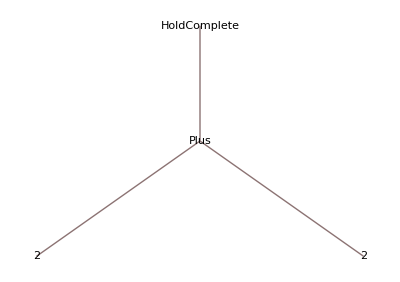

```mathematica
TreeForm@MakeExpression@StripBoxes@RowBox[{"2","+","2"}]
```